```mathematica
Initialization
```

```mathematica
(*Clear["Global`*"]*)
(*new experiment geometry*)
r=1000.;(*radius of curvature [mm]*)
d=60.;(*mirror diameter [mm]*)
l1=195.;(*distance between source and mirror [mm]*)
l2=185.;(*distance between mirror and detector [mm]*)
L=60.;(*length of the source [mm]*)
ψ=2ArcSin[d/(2r)];(*mirror apex angle*)
λ0 = 0.162;(*nm*)
α0=L^2/(16 l1^2)Sin[ψ]/(1-d/(2l1));
φ0=(L+d)/(2l1);
θ0 =0.003737816423136225;
```

```mathematica
Δ:=(#⟦1⟧Cos[#⟦4⟧]Cos[#⟦5⟧]+#⟦2⟧ Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-r) Sin[#⟦4⟧])^2-(#⟦1⟧)^2-(#⟦2⟧)^2-(#⟦3⟧)^2+2 r #⟦3⟧&
Intersect:=
{{x->#⟦1⟧-Cos[#⟦4⟧]Cos[#⟦5⟧](#⟦1⟧Cos[#⟦4⟧]Cos[#⟦5⟧]+#⟦2⟧ Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-r) Sin[#⟦4⟧]+Sqrt[Δ@#]),
y->#⟦2⟧-Cos[#⟦4⟧]Sin[#⟦5⟧](#⟦1⟧Cos[#⟦4⟧]Cos[#⟦5⟧]+#⟦2⟧ Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-r) Sin[#⟦4⟧]+Sqrt[Δ@#]),
z->#⟦3⟧-Sin[#⟦4⟧](#⟦1⟧Cos[#⟦4⟧]Cos[#⟦5⟧]+#⟦2⟧ Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-r) Sin[#⟦4⟧]+Sqrt[Δ@#])},
{x->#⟦1⟧-Cos[#⟦4⟧]Cos[#⟦5⟧](#⟦1⟧Cos[#⟦4⟧]Cos[#⟦5⟧]+#⟦2⟧ Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-r) Sin[#⟦4⟧]-Sqrt[Δ@#]),y->#⟦2⟧-Cos[#⟦4⟧]Sin[#⟦5⟧](#⟦1⟧Cos[#⟦4⟧]Cos[#⟦5⟧]+#⟦2⟧ Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-r) Sin[#⟦4⟧]-Sqrt[Δ@#]),
z->#⟦3⟧-Sin[#⟦4⟧](#⟦1⟧Cos[#⟦4⟧]Cos[#⟦5⟧]+#⟦2⟧ Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-r) Sin[#⟦4⟧]-Sqrt[Δ@#])}
}&
SphCross:=MaximalBy[Select[Intersect[#],π-ψ/2≤(ArcTan[z-r,√(x^2+y^2)]/.#)≤π&],y/.#&][[1]]&
IncVec:={Cos[#[[4]]]Cos[#[[5]]],Cos[#[[4]]]Sin[#[[5]]],Sin[#[[4]]]}&
IncAng:=Abs[π/2-VectorAngle[IncVec@#,{x,y,z-r}/.SphCross@#]]&
```

```mathematica
IndexRefr =Drop[Import[FileNames["*Al2O3.txt",NotebookDirectory[]][[1]],"Table"],2];
δ = Interpolation[IndexRefr[[All,{1,2}]],Method-> "Spline"];
γ = Interpolation[IndexRefr[[All,{1,3}]],Method-> "Spline"];
ε[λ_]:=1-δ[λ](*λ [nm]*)
εε[λ_]:=1-δ[λ]+ⅈ γ[λ](*λ [nm]*)
Rf:=Abs[Cos[#+ArcSin[Cos[#]/√εε[#2]]]/Cos[#-ArcSin[Cos[#]/√εε[#2]]]]^2&
TIS[θ0_,λ_,σ_]:=Rf[θ0,λ](1-Exp[-((4π σ Sin[θ0])/λ)^2])
Rs[θ0_,λ_,σ_]:=Rf[θ0,λ]Exp[-((4π σ Sin[θ0])/λ)^2]
Rspec[θ_,σ_,ψ_]:=Exp[-((4π σ Sin[θ])/λ0)^2 ψ/(2θ)]
```

```mathematica
Iimp[h_,r_:r,θ0_:θ0]:=If[h==0,1,2/θ0^2(1/2 θ0 √(θ0^2-2 h/r)-h/r Log[θ0+√(θ0^2-2 h/r)]+h/(2r)Log[2 h/r])]
Imp[x_,ImpH_,ImpR_:10r(1-Cos[2/3θ0])]:=Piecewise[{{√(((ImpH^2+ImpR^2)/(2ImpH))^2-x^2)-(ImpR^2-ImpH^2)/(2ImpH),-ImpR<x<ImpR}}]
Timp[ImpH_,r_:r,ImpR_:10r(1-Cos[2/3θ0])]:=Timp[ImpH,r,ImpR]=Re[NIntegrate[Iimp[Imp[x,ImpH,ImpR],r]/2/ImpR,{x,-ImpR,ImpR}]]
```

```mathematica
Ray Tracing C++ Demonstration
```

```mathematica
CPPTraceImport[name_]:={Import[name<>"/log_wolfram.xml"],CPPImport[name]}
CPPImport[name_]:=Join@@(Import/@FileNames[{"traces*","det_points*"},name])
DetCoord:={#[[1]]+l2 Cot[#[[5]]]-#[[2]] Cot[#[[5]]],l2,#[[3]]+l2 Csc[#[[5]]] Tan[#[[4]]]-#[[2]] Csc[#[[5]]] Tan[#[[4]]]}&
CPPDetData:=Prepend[#[[2;;3]],DetCoord@Last@#[[1]]]&/@#&
Options[TracePlot]={BoxRatios->{1,1,1/3},PlotRange->{{-1.5d/2,1.5d/2},{-1.5d/2,1.5d/2},{0,3(r-Cot[ψ/2]d/2)}},ImageSize->Large,AxesLabel->{x,y,z}};
TracePlot[trace_,opts:OptionsPattern[]]:=Show[ParametricPlot3D[{r Sin[θ]Cos[φ],r Sin[θ]Sin[φ],r(1+Cos[θ])},{θ,-π,-π+ψ/2},{φ,0,2π}],ParametricPlot3D[{l2,t,s},{t,-200,200},{s,0,1},PlotStyle->{Gray,Opacity[0.5]}],Graphics3D[{Green,PointSize[Small],Point[#[[1;;3]]]}]&/@trace[[1]],
If[trace[[2]]==0,Graphics3D[Line[#[[1;;3]]&/@trace[[1]]]],Graphics3D[Line[Append[#[[1;;3]]&/@trace[[1]],DetCoord[Last@trace[[1]]]]]]],Evaluate[FilterRules[Join[{opts},Options[TracePlot]],Options[Plot3D]]]]
ListTracePlot[mtrace_,opts:OptionsPattern[]]:=
Show[ParametricPlot3D[{r Sin[θ]Cos[φ],r Sin[θ]Sin[φ],r(1+Cos[θ])},{θ,-π,-π+ψ/2},{φ,0,2π}],ParametricPlot3D[{l2,t,s},{t,-200,200},{s,0,1},PlotStyle->{Gray,Opacity[0.5]}],
Graphics3D[{Line[Append[#[[1;;3]]&/@#[[1]],DetCoord[Last@#[[1]]]]],Opacity[0.001]}]&/@mtrace,
Map[Graphics3D[{Green,PointSize[0.006],Point[#[[1;;3]]]}]&,mtrace[[All,1]],{2}]//Flatten
,Evaluate[FilterRules[Join[{opts},Options[TracePlot]],Options[Plot3D]]]]
CPPTracePlot[mtrace_,opts:OptionsPattern[]]:=Show[ParametricPlot3D[#[[1]]+#[[2]] {Sin[θ]Cos[φ],Sin[θ]Sin[φ],Cos[θ]},{θ,-π,-π+ArcSin[#[[3]]/2/#[[2]]]},{φ,0,2π}]&@mtrace[[1,1]],ParametricPlot3D[#[[1]]+#[[2]] {Sin[θ]Cos[φ],Sin[θ]Sin[φ],Cos[θ]},{θ,0,ArcSin[#[[3]]/2/#[[2]]]},{φ,0,2π}]&/@Drop[mtrace[[1]],1],
ParametricPlot3D[{l2,t,s},{t,-200,200},{s,0,1},PlotStyle->{Gray,Opacity[0.5]}],
Graphics3D[Line[Append[#[[1;;3]]&/@#[[1]],DetCoord[Last@#[[1]]]]]]&/@mtrace[[2]],
Map[Graphics3D[{Green,PointSize[Small],Point[#[[1;;3]]]}]&,mtrace[[2,All,1]],{2}]//Flatten,
Evaluate[FilterRules[Join[{opts},Options[TracePlot]],Options[Plot3D]]]]
SetOptions[DensityHistogram,{ChartLegends->Automatic,ColorFunction->(Hue[0.7(1-#),1,0.85]&),ImageSize->Large,PlotRange->{{-20,20},{0,10}}}];
SetOptions[Histogram,{PlotRange->{{0,10},Automatic}}];
```

```mathematica
resscat[res_]:=Select[res,#[[3]]==1&]
resspec[res_]:=Select[res,#[[3]]==0&]
detpts[res_]:=res[[All,1,{1,3}]]
detx[res_]:=res[[All,1,3]]
```

```mathematica
Ray Tracing Results
```

```mathematica
res3d1000traces=Import[NotebookDirectory[]<>"results/RMSHeight_Series_3D_1000_traces.mx"];
```

```mathematica
res3dcor=Import[NotebookDirectory[]<>"results/CorrLength_Series_3D_1000.mx"];
```

```mathematica
res2d=Import[NotebookDirectory[]<>"results/RMSHeight_Series_2D.mx"];
```

```mathematica
res3d1000=Import[NotebookDirectory[]<>"results/RMSHeight_Series_3D_1000.mx"];
res3d1500=Import[NotebookDirectory[]<>"results/RMSHeight_Series_3D_1500.mx"];
res3d2000=Import[NotebookDirectory[]<>"results/RMSHeight_Series_3D_2000.mx"];
```

```mathematica
res3d1000sph=Import[NotebookDirectory[]<>"results/RMSHeight_Series_3D_1000_sph.mx"];
res3d1500sph=Import[NotebookDirectory[]<>"results/RMSHeight_Series_3D_1500_sph.mx"];
res3d2000sph=Import[NotebookDirectory[]<>"results/RMSHeight_Series_3D_2000_sph.mx"];
```

```mathematica
res3dcor4=CPPImport/@FileNames["*","D:\\OneDrive\\programming\\Ray-Tracing project\\results\\c++ results\\CorrLength_Series_R1000_4"];
```

```mathematica
Export[NotebookDirectory[]<>"results/CorrLength_Series_3D_1000_4.mx",res3dcor4];
```

```mathematica
Length/@res3dcor4
```

{121267,117304,115336,114835,114688,114494,115514,115430,116070,116988,118091,118995,120173,120773,122095,122270,123023,124749,125256,125572,126643,127185,127176,127190,128509}

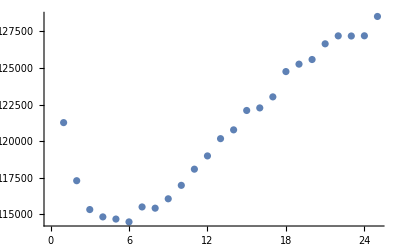

```mathematica
ListPlot[Length/@res3dcor4]
```

```mathematica
Length@(resscat@test3)
Length@(resspec@test3)
Length@(resscat@test4)
Length@(resspec@test4)
Length@(resscat@test5)
Length@(resspec@test5)
```

11425

49544

16599

41756

21428

36187

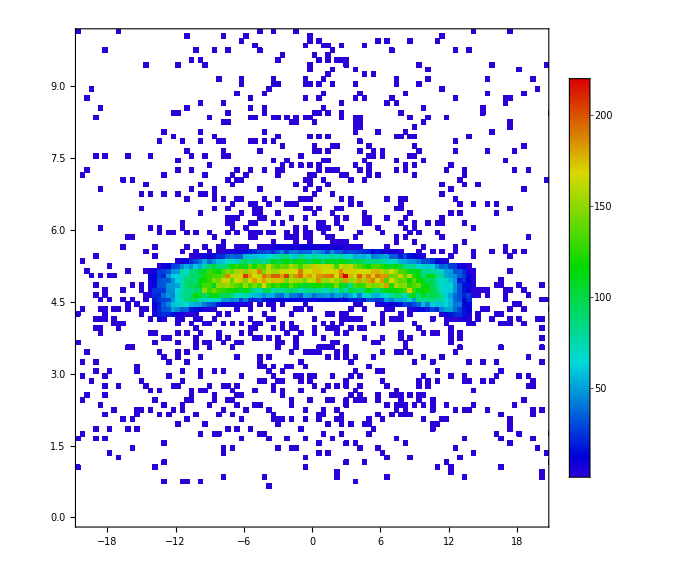

```mathematica
DensityHistogram[detpts@test,{{0.4},{0.1}}]
```

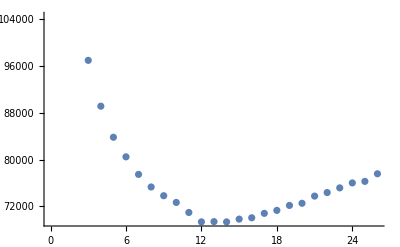

```mathematica
ListPlot[Length/@res3dcor]
```

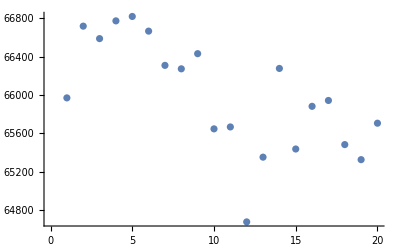

```mathematica
ListPlot[Length/@res3dcor2]
```

```mathematica
corl=Join[Range[0.15,1.35,0.15],Range[1.5,9.5,0.5]];
```

```mathematica
rmsh=Range[0,1.35,0.15];
```

```mathematica
bckgrd[res_,r_,rmsh_]:=bckgrd[res,r,rmsh]=Transpose[{rmsh,Length[Select[#,d/2/r l2+0.2<#[[1,3]]&]]/Length@#&/@res}]
fit[res_,r_,rmsh_]:=fit[res,r,rmsh]=FindFit[bckgrd[res,r,rmsh],TIS[a θ0,λ0,y]+bckgrd[res,r,rmsh][[1,2]],a,y]
fitmodel[res_,r_,rmsh_]:=Function[x,TIS[a θ0,λ0,x]+bckgrd[res,r,rmsh][[1,2]]/.fit[res,r,rmsh]]
errbckgrd[res_,r_]:=error[res,r]=1.5StandardDeviation[Length[Select[#,d/2/r l2+0.2<#[[1,3]]&]]/Length@#&/@Partition[#,Quotient[Length[#],8]]]&/@res
```

```mathematica
pow[res_,rmsh_]:=pow[res,rmsh]=Transpose[{rmsh,Length/@res/Length@res[[1]]}]
pow[res_,rmsh_,res0_]:=pow[res,rmsh,res0]=Prepend[Transpose[{rmsh,Length/@res/Length@res0}],{0,1}]
powspec[res_,rmsh_]:=powspec[res,rmsh]=Transpose[{rmsh,Length/@(resspec/@res)/Length@res[[1]]}]
powspec[res_,rmsh_,res0_]:=powspec[res,rmsh,res0]=Transpose[{rmsh,Length/@(resspec/@res)/Length@res0}]
errpowspec[res_]:=errpowspec[res]=1.5StandardDeviation[Length/@(resspec/@#)/Length@#[[1]]&/@Transpose[Partition[#,Quotient[Length[#],8]]&/@res]]
```

```mathematica
reshmin=Import[NotebookDirectory[]<>"results/ImpH_975nm_R_1000.mx"];
```

```mathematica
dimp=20r(1-Cos[2/3θ0]);
δbeam[R_,d_,θ0_]:=√(d^2-4 R^2 Sin[ArcSin[d/(2R)]-θ0/2]^2)/Cos[ArcSin[d/(2R)]-θ0/2]
σn[N_,dimp_,R_:r,d_:d,θ0_:θ0]:=√((δbeam[R,d,θ0]/dimp-1)/(N-δbeam[R,d,θ0]/(2dimp)+1))
I0[N_,dimp_,R_:r,d_:d,θ0_:θ0]:=(N dimp)/(1.1δbeam[R,d,θ0])
Πimp[x0_]:=√(1-x0)-x0 Log[1+√(1-x0)]+x0 Log[x0]/2
Πimp2[x0_]:=1-1/2x0-Log[2]x0+Log[x0] x0/2
hmin[σ_,R_:r,θ0_:θ0]:=-(6R θ0^2 σ)/ProductLog[-1,-3σ/ⅇ]
```

```mathematica
hmin[σn[Length@reshmin,dimp]]
```

0.000972824

```mathematica
I0[Length@reshmin,dimp]
σn[Length@reshmin,dimp]
```

354.859

0.0505714

```mathematica
N[Mean@Select[Transpose[{MovingAverage[#[[1]],2],#[[2]]}&@HistogramList[detpts[reshmin][[All,1]],{dimp}]],-δbeam[r,d,θ0]/4<#[[1]]<δbeam[r,d,θ0]/4&][[All,2]]]
N[StandardDeviation@Select[Transpose[{MovingAverage[#[[1]],2],#[[2]]}&@HistogramList[detpts[reshmin][[All,1]],{dimp}]],-δbeam[r,d,θ0]/4<#[[1]]<δbeam[r,d,θ0]/4&][[All,2]]]
N[StandardDeviation@#/Mean@#&@Select[Transpose[{MovingAverage[#[[1]],2],#[[2]]}&@HistogramList[detpts[reshmin][[All,1]],{dimp}]],-δbeam[r,d,θ0]/4<#[[1]]<δbeam[r,d,θ0]/4&][[All,2]]]
```

355.958

20.8423

0.0585525

```mathematica
292./355.9583333333333
(355.4642857142857-292.)/19.75566101151037
```

0.820321

3.21246

```mathematica
Ray Tracing Results Examination
```

```mathematica
trace1000=Import[NotebookDirectory[]<>"RMSHeight_Series_1000_traces.mx"];
```

```mathematica
Length/@(resscat/@trace1000)
```

{0,1006,3688,7760,12552,17808,23323,28626,33289,37074}

```mathematica
Nr[d_,r_,θ_]:=ArcSin[d/(2r)]/θ+1
```

```mathematica
Mean[IncAng/@trace1000[[1,All,1,1]]/θ0]
```

0.775939

```mathematica
Mean[IncAng/@trace1000[[2,All,1,1]]/θ0]
```

0.775471

```mathematica
Mean[IncAng/@trace1000[[5,All,1,1]]/θ0]
```

0.782985

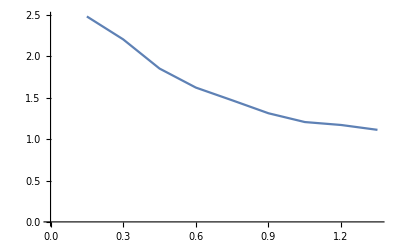

1.6041

```mathematica
avang=Mean[IncAng/@resscat[#][[All,1,1]]/θ0]&/@trace1000[[2;;10]];
ListPlot[{Range[0.15,1.35,0.15],avang}//Transpose,Joined->True]
Mean@avang
```

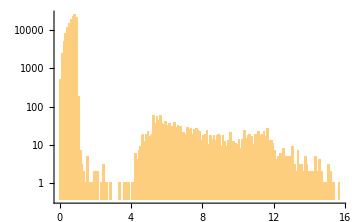
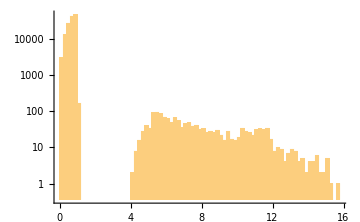
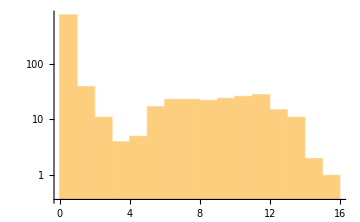

```mathematica
Row[{Histogram[IncAng/@trace1000[[2,All,1,1]]/θ0,PlotRange->{{0,16},{0,20000}},ImageSize->Medium],
Histogram[IncAng/@resspec[trace1000[[2]]][[All,1,1]]/θ0,{0.2},PlotRange->{{0,16},{0,20000}},ImageSize->Medium],
Histogram[IncAng/@resscat[trace1000[[2]]][[All,1,1]]/θ0,PlotRange->{{0,16},{0,20000}},ImageSize->Medium]}]
```

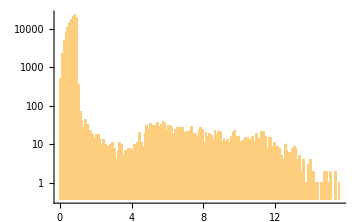
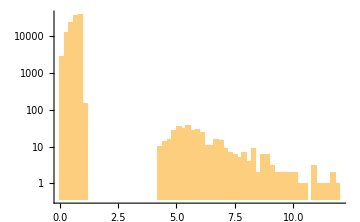
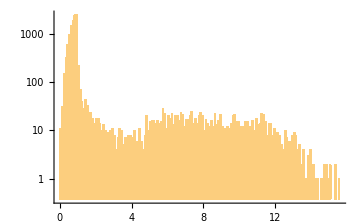

```mathematica
Row[{Histogram[IncAng/@trace1000[[5,All,1,1]]/θ0,PlotRange->{{0,16},{0,20000}},ImageSize->Medium],
Histogram[IncAng/@resspec[trace1000[[5]]][[All,1,1]]/θ0,{0.2},PlotRange->{{0,16},{0,20000}},ImageSize->Medium],
Histogram[IncAng/@resscat[trace1000[[5]]][[All,1,1]]/θ0,PlotRange->{{0,16},{0,20000}},ImageSize->Medium]}]
```

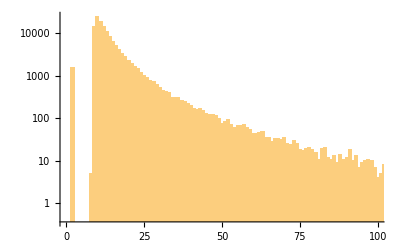

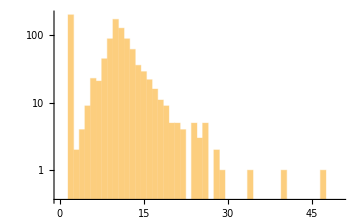
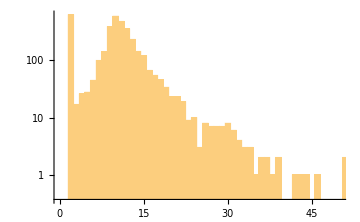
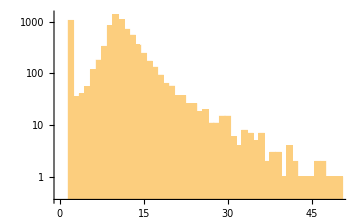

```mathematica
Histogram[Length/@resspec[trace1000[[2]]][[All,1]],{1},PlotRange->{{0,100},All}]
Row[Histogram[Length/@resscat[#][[All,1]],{1},PlotRange->{{0,50},Full},ImageSize->Medium]&/@trace1000[[2;;4]]]
```

```mathematica
avn=Mean[Length/@resscat[#][[All,1]]]&/@trace1000[[2;;10]];
```

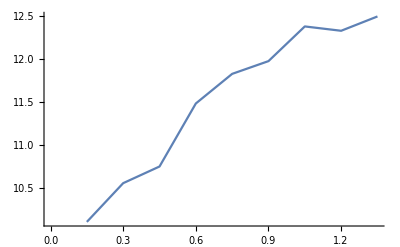

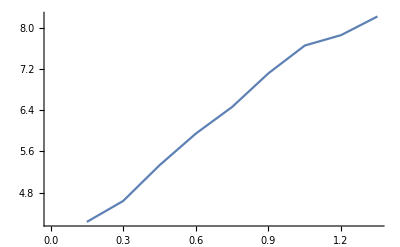

```mathematica
ListPlot[{Range[0.15,1.35,0.15],avn}//Transpose,Joined->True]
ListPlot[{Range[0.15,1.35,0.15],Nr[60,1000,# θ0]&/@avang}//Transpose,Joined->True]
```

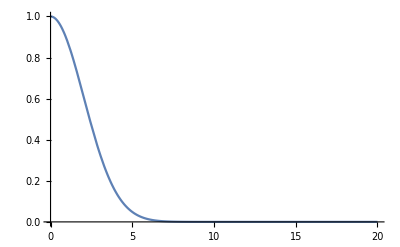

```mathematica
Plot[Rs[x θ0, λ0, 1.2]/Rf[x θ0,λ0],{x,0,20},PlotRange->{Automatic,{0,1}}]
```

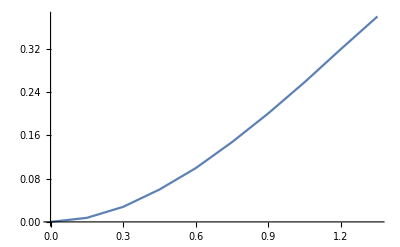

```mathematica
ListPlot[{rmsh,Length/@(resscat/@trace1000)/Length/@trace1000}//Transpose,Joined->True]
```

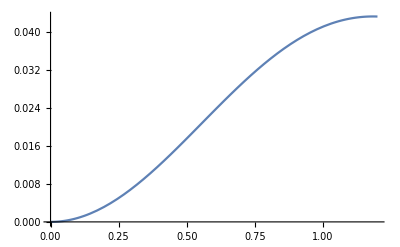

```mathematica
Plot[Exp[-((4π σ Sin[θ0])/λ0)^2(Nr[60,1000,θ0]-1)](1-Exp[-((4π σ Sin[θ0])/λ0)^2]),{σ,0,1.2}]
```

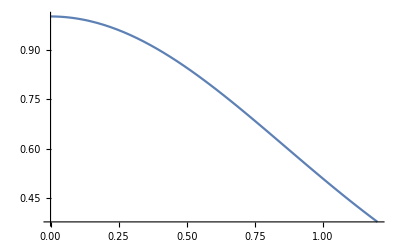

```mathematica
Plot[Exp[-((4π σ Sin[θ0])/λ0)^2 ψ/(2θ0)],{σ,0,1.2}]
```

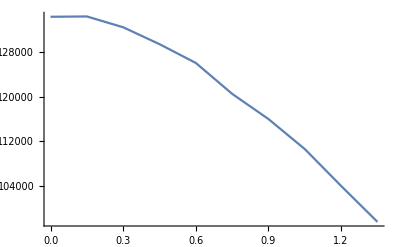

```mathematica
ListPlot[{rmsh,Length/@trace1000}//Transpose,Joined->True]
```

```mathematica
angdist=Import[NotebookDirectory[]<>"angles_plane2D.mx"];
```

```mathematica
Mean[angdist]/θ0
Mean[IncAng/@trace1000[[1,All,1,1]]]/θ0
```

0.658674

0.775939

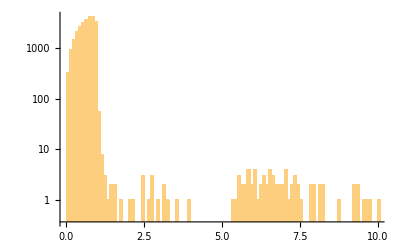

```mathematica
Histogram[angdist/θ0]
```

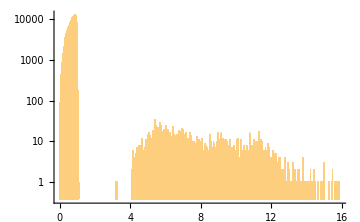

```mathematica
Histogram[IncAng/@trace1000[[1,All,1,1]]/θ0,PlotRange->{{0,16},{0,20000}},ImageSize->Medium]
```

```mathematica
Mean[IncAng/@Select[trace1000[[1,All,1,1]],IncAng@#<2θ0&]]/θ0
```

0.681143

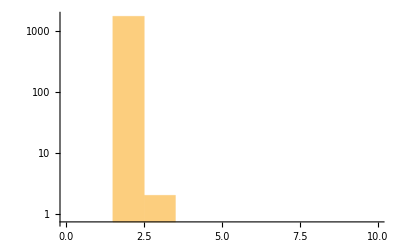

```mathematica
Histogram[Length/@Select[trace1000[[1,All,1]],IncAng[#[[1]]]>2θ0&]]
```